# Лабораторная работа №7

## Математические модели процессов переноса частиц вещества

Мат. моделирование динамических процессов 1
БГУ, ММФ, 3 курс, 6 семестр
специальность Компьютерная математика и системный анализ
май 2022
ММФ, КМ и СА, доц. Лаврова О.А., доц. Щеглова Н.Л.

## Аналитическое решение для уравнения переноса

Уравнение переноса является частным случаем уравнения непрерывности, когда скорость движения частиц вещества постоянная u=const. Построим аналитическое решение уравнения переноса для заданной скорости движения частиц u=u_0=const, и заданной начальной плотности частиц r(x,0)=r0(x) в общем виде.

```mathematica
ClearAll[r,r0]
```

```mathematica
DSolve[{D[r[x,t],t]+Subscript[u, 0] D[r[x,t],x]==0,r[x,0]==r0[x]},r[x,t],{x,t}]
```

{{r[x,t]→r0[x-t u_0]}}

Построим аналитическое решение для явно заданного значения скорости движения частиц u_0 и явно заданной функции начальной плотности частиц r0(x)

```mathematica
Subscript[u, 0]=1;r0[x_]:=ⅇ^(-x^2);
```

```mathematica
r=r /.DSolve[{D[r[x,t],t]+Subscript[u, 0] D[r[x,t],x]==0,r[x,0]==r0[x]},r,{x,t}]//Flatten//First
```

Function[{x,t},ⅇ^(-(-t+x)^2)]

Решение представляет собой бегущую волну (traveling wave), т.е. волну, которая движется без изменения формы. Для рассматриваемого примера волна движется вправо, т.к. скорость движения частиц вещества положительна, u_0>0.

```mathematica
Plot3D[r[x,t],{x,-2,10},{t,0,10},AxesLabel->Automatic]
```

-Graphics3D-

Покажем, что пространственный профиль ⅇ^(-x^2) движется без искажений со скоростью u_0=1>0 вправо

```mathematica
Manipulate[Plot[r[x,t],{x,-2,10},PlotRange->{Automatic,{0,1}}],{t,0,10}]
```

Построим характеристики или характеристические кривые, которые являются линиями уровня для функции плотности частиц

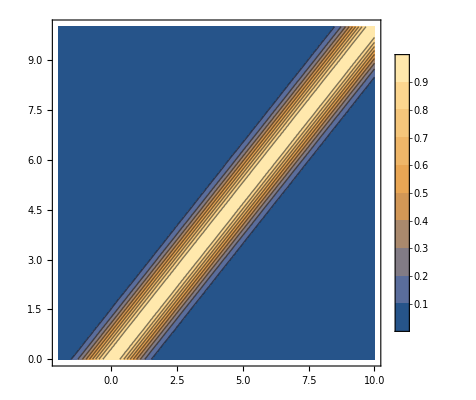

```mathematica
ContourPlot[r[x,t],{x,-2,10},{t,0,10},PlotLegends->Automatic]
```

Для уравнения переноса характеристиками являются параллельные прямые x-u_0 t=const

## Аналитическое решение для невязкого уравнения Бюргерса

Невязкое уравнение Бюргерса является частным случаем уравнения непрерывности, когда скорость скорость движения частиц вещества равна плотности вещества u=ρ. Построим аналитическое решение уравнения переноса в общем виде задания начального условия

```mathematica
ClearAll[r0]
```

```mathematica
DSolve[D[r1[x,t],t]+r1[x,t]D[r1[x,t],x]==0,r1[x,t],{x,t}]
```

Solve[r1[x,t]==C[1][x-t r1[x,t]],r1[x,t]]

Определим начальное условие, которое соответствует моделированию дорожного трафика с учетом работы светофора, расположенного в точке x=0, при смене цвета светофора с красного на зеленый в момент времени t=0. При этом полагается, что перед светофором плотно стоят машины, а после светофора дорога пустая.

```mathematica
r0[x_]:=Which[x≤ 0,-1 (*пробка*),x>0,1 (*пустая дорога*)];
```

```mathematica
r1=r1/.Solve[r1==r0[x-t r1]&&t≥0,r1]//FullSimplify
```

{ConditionalExpression[-1, t>0&&t+x<0],ConditionalExpression[1, 0<t<x]}

```mathematica
Plot3D[r1,{x,-10,10},{t,0,10},AxesLabel->Automatic]
```

-Graphics3D-

Решение является разрывным в точке x=0, t=0 в силу начального условия. При этом решение неопределено при -t<x<t.

Доопределим решение при -t<x<t, аппроксимируя плотность непрерывной функцией

```mathematica
r2[x_,t_?NonNegative]:=Which[x≤-t,-1 (*пробка*),-t<x<t,x/t,x>t,1 (*пустая дорога*)];
```

```mathematica
Plot3D[r2[x,t],{x,-10,10},{t,0,10},AxesLabel->Automatic]
```

-Graphics3D-

Построим характеристики или характеристические кривые, которые являются линиями уровня для плотности

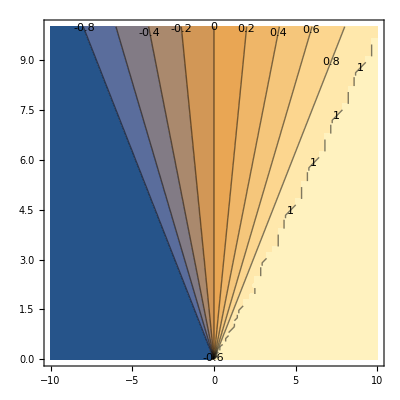

```mathematica
ContourPlot[r2[x,t],{x,-10,10},{t,0,10},ContourLabels->True]
```

По графику видно, что характеристические линии являются прямыми линиями для -1<ρ<1 и пересекаются в точке при x=0, t=0. В отличие от невязкого урвнения Бюргера в уравнении переноса характеристические линии всегда являются параллельными.

## Задание 1. Перенос загрязнения в притоке реки

### Содержательная постановка задачи

[1, раздел 4.1 стр. 93--97] В притоке реки за 10^4 м до впадения притока в реку происходит выброс частиц химического вещества в воду в течении 5 мин. Начальное содержание частиц химического вещества в воде составляет 10%, т.е. плотность субстанции в воде равна 0.1 (мин*м)^-1 в период выброса. Скорость движения частиц вещества в месте выброса определяется скоростью движения воды и равна 60 м/мин. Приток расширяется и скорость движения воды падает на 20% в месте впадения притока в реку. Дополнительно нужно учесть, что каждую минуту 1% химического вещества оседает на дно.

### Концептуальная постановка задачи

Приток реки описывается прямой линией. Совмещаем ось Ox  с направлением движения воды в притоке реки. Полагаем, что выброс химического вещества осуществляется в точке x=-a, и за 5 мин химическое вещество с плотностью γ=0.1 (мин*м)^-1 заполняет отрезок [-a,0] притока реки. С учетом того, что скорость движения частиц вещества в момент выброса u_0=60 м/мин, не учитывая расширения притока в течении 5 мин, имеем, что a=u_0*5 мин =300м. Обозначим через x=L место впадения притока в реку. По условию задачи L=10^4 м.

Полагаем, что плотность химического вещества описывается функцией ρ=ρ(x,t), где 0≤x≤L соответствует моделированию движения только в притоке реки .

Полагаем, что выброс химического вещества заканчивается в момент времени t=0. Тогда начальное условие ρ(x,0)=ρ_0(x) для плотности химического вещества задается следующей функцией: ρ_0(x)=γ для x∈[-a,0] и ρ_0(x)=0 для x≥0.

Из-за расширения притока скорость движения частиц u будет зависеть от x. Известно, что в точке x=0 скорость u(x)=u_0 и при x=L скорость потока падает на 20%. Тогда можно построить зависимость u(x)=u_0(1-α x), где α=0.2/Lм^-1, x≥0.

Оседание химической субстанции на дно реки задается дополнительным слагаемым σ ρ(x,t) в левой части уравнения непрерывности, где β=0.01 мин^-1.

### Задание 1.1 (Математическая модель)

Постройте математическую модель переноса частиц химического вещества в притоке реки для 0≤x≤L и t≥0 на основе концептуальной постановки задачи.

Математическая модель переноса частиц химического вещества в притоке реки для 0≤x≤L и t≥0 на основе концептуальной постановки задачи

ρ_t + [u_0 (1 - α x) ρ]_x  ==  -β ρ,
ρ (x, 0) = ρ_0(x),
t ≥ 0,
0≤x≤L

### Задание 1.2 (Аналитическое решение)

Постройте аналитическое решение математической модели из Задания 1.1 с помощью метода характеристик.

Сравните с аналитическим решением, полученным с помощью функции DSolve.

Аналитическое решение математической модели из Задания 1.1 с помощью метода характеристик

ρ_t + [u_0 (1 - α x) ρ]_x  ==  -β ρ ; (*)

Получим ДУ для x(s), t(s), где s :> ρ(x(s), t(s)), установив отношение
d/ds ρ(x(s),t(s)) = ρ_t dt/ds+ρ_x dx/ds;

Учитывая последнее и ДУ (*) 

dρ/dt + u_0 (1 - α x)dρ/dx ==  (u_0 α -β) ρ ;

Пусть dt/ds=1, dx/ds= u_0 (1 - α x), dρ/ds = (u_0 α -β)ρ

В силу начальный условий, ДУ можно решить явно. Из-за того, что dt = ds получаем:

dx/dt= u_0 (1 - α x), x(0)=x_0,
dρ/dt =(u_0 α -β)ρ, ρ(0) = ρ_0 (**)

Тогда из последнего получим
dx/(1 - α x) = u_0 dt
dρ/ρ = (u_0 α -β) dt

Решая два последних ДУ и учитывая  условия из (**), мы получаем
x(t) = 1/α(1 - ⅇ^(-α u_0 t) [1-α x_0] )
ρ(t)= ρ_0ⅇ^((u_0 α  - β) t)

В силу начальных условий из (*) получим:
x_0 = 1/α(1 - ⅇ^(α u_0 t) [1-α x_0] )

Тогда аналитическое решение математической модели из (*) получается
ρ(x,t) = ρ_0[1-ⅇ^(α u_0 t) (1-α x)] ⅇ^(-(u_0 α  - β) t)

Аналитическое решение математической модели из Задания 1.1 с помощью функции DSolve

```mathematica
sol=(DSolve[{D[ρ[x,t],t]+ D[(u0(1-α x) ρ[x,t]),x]==-β ρ[x,t],ρ[x,0]==Piecewise[{{γ,-a≤x≤0}},0]},ρ,{x,t}]//Values)⟦1,1⟧
```

Function[{x,t},ⅇ^(t u0 α) (u0-u0 x α)^(β/(u0 α)) (ⅇ^(t u0 α) (u0-u0 x α))^(-β/(u0 α)) (Piecewise[{{γ, -a≤(u0-ⅇ^(t u0 α) (u0-u0 x α))/(u0 α)≤0}, {0, True}}])]

### Задание 1.3 (Время впадения химического вещества в реку)

Оцените временной интервал, в течение которого химическое вещество будет попадать в реку. Для этого по аналитическому решению для плотности химического вещества необходимо найти временной интервал, при котором плотность химического вещества в месте впадения притока в реку положительна, ρ(x=L,t)>0 . 

Сравните с результатом из [1, раздел 4.1 стр. 93--97], 186 мин ≤ t^*≤191 мин.

```mathematica
L=10^4;
γ=0.1;
a=300;
α=0.2/L;
u0=60;
β=0.01;
time1=Quiet@Reduce[sol[L,t]>0,t,Reals]
```

185.953≤t≤190.938

### Задание 1.4 (Количество вещества, которое попадет в реку)

Количество химического вещества, попавшего в приток реки в месте выброса, вычисляется по формуле ∫_0^(5 мин) γⅆt=0.5 м^-1. 

Вычислите количество химического вещества, которое попадет в реку. Для этого необходимо вычислить интеграл по времени от функции плотности в месте впадения притока в реку ρ(L,t) по временному интервалу из Задания 1.3. 

Вычислите, какое количество химического вещества осядет на дно до момента впадения в реку?

```mathematica
time1⟦1⟧
time1⟦5⟧
```

185.953

190.938

Количество химического вещества, которое попадет в реку

```mathematica
NIntegrate[sol[L,t],{t,time1⟦1⟧,time1⟦5⟧}]
```

0.0949524

Количество химического вещества осядет на дно до момента впадения в реку

```mathematica
0.5 - β NIntegrate[sol[L,t],{t,time1⟦1⟧,time1⟦5⟧}]
```

0.49905

## Задание 2. Перенос загрязнения в сужающемся притоке реки

Выполните Задания 1.1--1.4 при изменении одного из условий в концептуальной поставке задачи: приток реки сужается и скорость движения воды увеличивается на 20% в месте впадения притока в реку.

### Задание 2.1 (Аналитическое решение)

Математическая модель переноса частиц химического вещества в притоке реки для 0≤x≤L и t≥0 на основе концептуальной постановки задачи при сужении притока реки и увеличении скорости движения воды  на 20% в месте впадения притока в реку

ρ_t + [u_0 (1 + α x) ρ]_x  ==  -β ρ,
t(0)=t_(0,)
x(0) = x_0,
ρ (x, 0) = ρ_0(x),                                                      (***)
t ≥ 0,
0≤x≤L

Аналитическое решение математической модели из (***) с помощью метода характеристик

ρ_t + [u_0 (1 + α x) ρ]_x  ==  -β ρ ; (1)

Получим ДУ для x(s), t(s), где s :> ρ(x(s), t(s)), установив отношение
d/ds ρ(x(s),t(s)) = ρ_t dt/ds+ρ_x dx/ds;

Учитывая последнее и ДУ (1) 

dρ/dt + u_0 (1 + α x)dρ/dx ==  -(u_0 α +β) ρ ;

Пусть dt/ds=1, dx/ds= u_0 (1 + α x), dρ/ds = -(u_0 α +β)ρ

В силу начальный условий, ДУ можно решить явно. Из-за того, что dt = ds получаем:

dx/dt= u_0 (1 + α x), x(0)=x_0,
dρ/dt =-(u_0 α +β)ρ, ρ(0) = ρ_0 (2)

Тогда из последнего получим
dx/(1 + α x) = u_0 dt
dρ/ρ = -(u_0 α +β) dt

Решая два последних ДУ и учитывая  условия из (2), мы получаем
x(t) = 1/α(1 - ⅇ^(α u_0 t) [1+α x_0] )
ρ(t)= ρ_0ⅇ^(-(u_0 α  + β) t)

В силу начальных условий из (***) получим:
x_0 = 1/α(1 - ⅇ^(α u_0 t) [1+α x_0] )

Тогда аналитическое решение математической модели из (***) получается
ρ(x,t) = ρ_0[1-ⅇ^(α u_0 t) (1+α x)] ⅇ^(-(u_0 α  + β) t)

Аналитическое решение математической модели из (***) с помощью функции DSolve

```mathematica
ClearAll[L,γ,a,α,u0,β];
sol1=(DSolve[{D[ρ[x,t],t]+ D[(u0(1+α x) ρ[x,t]),x]==-β ρ[x,t],ρ[x,0]==Piecewise[{{γ,-a≤x≤0}},0]},ρ,{x,t}]//Values)⟦1,1⟧
```

Function[{x,t},ⅇ^(-t u0 α) (u0+u0 x α)^(-β/(u0 α)) (u0-ⅇ^(-t u0 α) (u0+u0 x α) (-1+(ⅇ^(t u0 α) u0)/(u0+u0 x α)))^(β/(u0 α)) (Piecewise[{{γ, -a≤-(ⅇ^(-t u0 α) (u0+u0 x α) (-1+(ⅇ^(t u0 α) u0)/(u0+u0 x α)))/(u0 α)≤0}, {0, True}}])]

### Задание 2.2 (Время впадения химического вещества в реку)

```mathematica
L=10^4;
γ=0.1;
a=300;
α=0.2/L;
u0=60;
β=0.01;
time2=Quiet@Reduce[sol1[L,t]>0,t,Reals]
```

151.935≤t≤156.95

### Задание 2.3 (Количество вещества, которое попадет в реку)

```mathematica
time2⟦1⟧
time2⟦5⟧
```

151.935

156.95

Количество химического вещества, которое попадет в реку

```mathematica
NIntegrate[sol1[L,t],{t,time2⟦1⟧,time2⟦5⟧}]
```

0.0889429

Количество химического вещества осядет на дно до момента впадения в реку

```mathematica
0.5 -β NIntegrate[sol1[L,t],{t,time2⟦1⟧,time2⟦5⟧}]
```

0.499111

## Задание 3. Моделирование дорожного трафика

Дорожный трафик можно описывать с помощью уравнения непрерывности для плотности автомобилей ρ(x,t) в предположении движения автомобилей по прямой линии и заданной скорости движения автомобилей, которая зависит только от плотности автомобилей v(ρ)=v_max(1-ρ/ρ_max).

В безразмерных переменных математическая модель записывается в виде невязкого уравнения Бюргерса

(∂ρ)/(∂t)+ρ (∂ρ)/(∂x)==0

и начального условия

ρ(x,0)==ρ_0(x).

Отметим, что в безразмерных переменных плотность автомобилей изменяется от -1 до 1, -1≤ρ(x,t)≤1 , где значение ρ=-1 соответствует пробке на дороге, ρ=0 -- умеренному трафик, ρ=1 -- пустой дороге.

### Задание 3.1 (Аналитическое решение)

Постройте аналитическое решение математической модели для невязкого уравнения Бюргерса с помощью метода характеристик для  начального условия вида

Аналитическое решение математической модели для невязкого уравнения Бюргерса с помощью метода характеристик для  начального условия

(∂ρ)/(∂t)+ρ (∂ρ)/(∂x)==0, (*)
ρ(x,0)==ρ_0(x).

Полагаем, что t=t(s), x=x(s). Тогда ρ = ρ(x(s),t(s)).
Воспользуемся соотношением 
dρ/ds=dρ/dt dt/ds + dρ/dx dx/ds;

Полагаем, что dρ/ds = 0  ==> dt/ds=1, dx/ds=ρ; 

Составим задачу Коши для системы ОДУ

dρ/ds = 0,     ρ(0) =ρ_0(x_0)					dρ/dt=0,     ρ(0) =ρ_0(x_0)
                                                            dt = ds
dt/ds=1,     t(0) = 0                              ====>
	
dx/ds = ρ,   x(0) = x_0						dx/dt=ρ,    x(0) = x_0

	ρ(t) = ρ_0(x_0)
====> 					====>  
	x(t) - x_0(t) = ρ_0(x_0) t   
	
Аналитическое решение для модели (*) имеет вид
	ρ(x,t) = ρ_0(x - ρ(x,t) t)

ρ_0(x)=1 при  x<0,

ρ_0(x)=1-x при  0≤x≤1,

ρ_0(x)=0 при x>1.

Изобразите график плотности автомобилей. 

Предложите физическую интерпретацию построенного решения.

```mathematica
DSolve[D[ρ[x,t],t]+ρ[x,t]D[ρ[x,t],x]==0,ρ[x,t],{x,t}]
```

Solve[ρ[x,t]==C[1][x-t ρ[x,t]],ρ[x,t]]

```mathematica
ClearAll[ro];
ro[x_,t_?NonNegative]:=Which[x<0,1 (*пустая дорога*),0≤x≤1,1-x,x>1,0 (*умеренный трафик*)];
Plot3D[ro[x,t],{x,-10,10},{t,0,10},AxesLabel->Automatic]
```

-Graphics3D-

Модель плотности автомобилей для невязкого уравнения Бюргерса 
(∂ρ)/(∂t)+ρ (∂ρ)/(∂x)==0, 
ρ(x,0)==ρ_0(x).
 
 Будет иметь решение вида 
 ρ(x,t) = ρ_0(x - ρ(x,t) t)
 
 И исходя из вышепоказанного графика,  модель имеет непрерывную функцию, а также для ρ_0(x) справделива следующая система
:
 ρ_0(x)=1 при  x<0,
 ρ_0(x)=1-x при  0≤x≤1,
 ρ_0(x)=0 при x>1.

Построим характеристики или характеристические кривые, которые являются линиями уровня для плотности

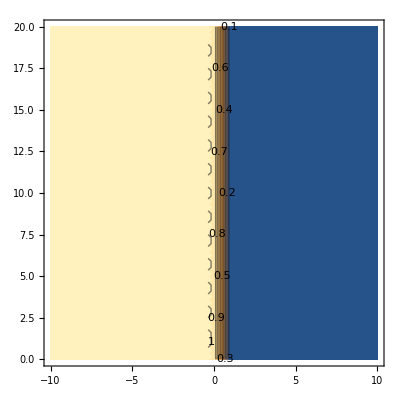

```mathematica
ContourPlot[ro[x,t],{x,-10,10},{t,0,20},ContourLabels->True]
```

## Задание 4. Двусолитонные решения Кортевега-де Фриза

Солитон -- это уединенная волна, которая сохраняет свою форму и скорость при движении и столкновении с себе подобными уединенными волнами.

Уравнение Кортевега-де Фриза (построено в 1895 году)

(∂^3 u(x,t))/(∂x^3)+(∂u(x,t))/(∂t)+6 u(x,t) (∂u(x,t))/(∂x)==0

описывает отклонение свободной поверхности воды от положения равновесия при определенных предположениях. В частности, волна должна быть длинной, т.е. длина волны существенно больше глубины слоя воды.

Двусолитонное решение уравнения Кортевега-де Фриза строится по формуле, см., например, [3, стр. 580]

u(x,t)=2(∂^2 log(F(x,t)))/(∂x^2),F(x,t)=1+f_1(x,t)+f_2(x,t)+A f_2(x,t) f_1(x,t),

где f_i(x,t)=ⅇ^(θ_i(x,t)), θ_i(x,t)=-t a_i^3+x a_i+δ_i, A=((a_1-a_2)/(a_1+a_2))^2.

### Задание 4.1 (Аналитическое односолитонное решение)

Постройте аналитическое решение уравнения Кортевега-де Фриза с помощью функции DSolve.

Продемонстрируйте, что пространственный профиль решения уравнения сохраняется во времени, т.е. решение представляет собой бегущую волну.

```mathematica
(Quiet@DSolve[{D[u[x,t],{x,3}]+D[u[x,t],t]+6u[x,t]D[u[x,t],x]==0},u[x,t],{x,t}]//Values//Flatten)⟦1⟧
```

-(-8 C[1]^3+C[2]+12 C[1]^3 Tanh[x C[1]+t C[2]+C[3]]^2)/(6 C[1])

```mathematica
Manipulate[
Plot3D[-(-8 C1^3+C2+12 C1^3 Tanh[x C1+t C2+C3]^2)/(6 C1),{x,-10,10},{t,0,10},ImageSize->Large],
{{C1,-0.4},-3,3,0.01,Appearance->"Labeled"},
{{C2,0.4},-3,3,0.01,Appearance->"Labeled"},
{{C3,-0.9},-3,3,0.01,Appearance->"Labeled"}]
```

```mathematica
Manipulate[
ContourPlot[-(-8 C1^3+C2+12 C1^3 Tanh[x C1+t C2+C3]^2)/(6 C1),{x,-10,10},{t,0,20},ImageSize->Large],
{{C1,-0.4},-3,3,0.01,Appearance->"Labeled"},
{{C2,0.4},-3,3,0.01,Appearance->"Labeled"},
{{C3,-0.9},-3,3,0.01,Appearance->"Labeled"}]
```

### Задание 4.2 (Аналитическое двусолитонное решение)

Покажите, что аналитическое решение вида (2) удовлетворяет уравнению Кортевега-де Фриза (1).

u(x,t)=2(∂^2 log(F(x,t)))/(∂x^2),F(x,t)=1+f_1(x,t)+f_2(x,t)+A f_2(x,t) f_1(x,t),

где f_i(x,t)=ⅇ^(θ_i(x,t)), θ_i(x,t)=-t a_i^3+x a_i+δ_i, A=((a_1-a_2)/(a_1+a_2))^2.

(∂^3 u(x,t))/(∂x^3)+(∂u(x,t))/(∂t)+6 u(x,t) (∂u(x,t))/(∂x)==0

```mathematica
ClearAll[Θ,f,F,u];
A=((Subscript[a, 1]-Subscript[a, 2])/(Subscript[a, 1]+Subscript[a, 2]))^2;
Θ[i_]:=-t Subscript[a, i]^3+x Subscript[a, i]+Subscript[δ, i];
f[i_]:=ⅇ^Θ[i];
F=1+f[1]+f[2]+A f[2]f[1]
u=2D[Log[F],{x,2}]
D[u,{x,3}]+D[u,t]+6u D[u,x]//Simplify
```

1+ⅇ^(x 300_1-t 300_1^3+δ_1)+ⅇ^(x 300_2-t 300_2^3+δ_2)+(ⅇ^(x 300_1-t 300_1^3+x 300_2-t 300_2^3+δ_1+δ_2) (300_1-300_2)^2)/(300_1+300_2)^2

2 ((ⅇ^(x 300_1-t 300_1^3+δ_1) 300_1^2+ⅇ^(x 300_1-t 300_1^3+x 300_2-t 300_2^3+δ_1+δ_2) (300_1-300_2)^2+ⅇ^(x 300_2-t 300_2^3+δ_2) 300_2^2)/(1+ⅇ^(x 300_1-t 300_1^3+δ_1)+ⅇ^(x 300_2-t 300_2^3+δ_2)+(ⅇ^(x 300_1-t 300_1^3+x 300_2-t 300_2^3+δ_1+δ_2) (300_1-300_2)^2)/(300_1+300_2)^2)-((ⅇ^(x 300_1-t 300_1^3+δ_1) 300_1+ⅇ^(x 300_2-t 300_2^3+δ_2) 300_2+(ⅇ^(x 300_1-t 300_1^3+x 300_2-t 300_2^3+δ_1+δ_2) (300_1-300_2)^2)/(300_1+300_2))^2)/((1+ⅇ^(x 300_1-t 300_1^3+δ_1)+ⅇ^(x 300_2-t 300_2^3+δ_2)+(ⅇ^(x 300_1-t 300_1^3+x 300_2-t 300_2^3+δ_1+δ_2) (300_1-300_2)^2)/(300_1+300_2)^2)^2))

0

Условие (4) выполнено, значит решение построено правильно. Соответственно, аналитическое решение вида (3) удовлетворяет уравнению Кортевега-де Фриза (4)

### Задание 4.3 (Столкновение двух солитонов)

Осуществите динамическую визуализацию двусолитонного решения уравнения Кортевега-де Фриза при различных значениях параметров a_1, a_2, δ_1, δ_2. 

Подберите значения параметров, соответствующие столкновению двух солитонов. 

Продемонстрируйте, что пространтсвенный профиль каждого из солитонов сохраняется после их столкновения.

Значения параметров, соответствующие столкновению двух солитонов, возьмем, к примеру:
a_1 = - 0.73;  a_2 = 2.24;
δ_1 = 8.45;  δ_2 = 6.66;

```mathematica
Mesh
```

```mathematica
Manipulate[Plot3D[u/.{Subscript[a, 1]->a1,Subscript[a, 2]->a2,Subscript[δ, 1]->δ1,Subscript[δ, 2]->δ2},{x,-20,20},{t,0,20},ImageSize->Large],{{a1,0.3},-5,5,0.01,Appearance->"Labeled"},
{{a2,0.3},-5,5,0.01,Appearance->"Labeled"},
{{δ1,0.5},-5,5,0.01,Appearance->"Labeled"},
{{δ2,0.5},-5,5,0.01,Appearance->"Labeled"}]
```

```mathematica
Manipulate[ContourPlot[u/.{Subscript[a, 1]->a1,Subscript[a, 2]->a2,Subscript[δ, 1]->δ1,Subscript[δ, 2]->δ2},{x,-20,20},{t,0,20},ImageSize->Large],{{a1,-0.87},-10,10,0.01,Appearance->"Labeled"},
{{a2,1.98},-10,10,0.01,Appearance->"Labeled"},
{{δ1,8.74},-10,10,0.01,Appearance->"Labeled"},
{{δ2,-4.65},-10,10,0.01,Appearance->"Labeled"}]
```

## Задание 5 (необязательное). Моделирование дорожного трафика в туннеле

[2, стр. 253] Дорожный трафик в туннеле можно описывать с помощью уравнения непрерывности для плотности автомобилей ρ(x,t) в предположении движения по прямой линии и заданной скорости потока, зависящей от плотности v(ρ)=v_max при 0≤ρ≤ρ_c и v(ρ)=(v_max log(ρ_max/ρ))/(log(ρ_max/ρ_c)) при ρ_c≤ρ≤ρ_max.

Полагаем, что въезд в туннель расположен в точке x=0 и автомобили при максимальной плотности ожидают открытия туннеля в момент времени t=0.

ρ_0(x)=ρ_max при  x<0,

ρ_0(x)=0 при x>0.

### Задание 5.1 (Математическая модель)

Сформулируйте математическую модель задачи о дорожном трафике в туннеле.

### Задание 5.2 (Аналитическое решение)

Постройте решение математической модели, сформулированной в Задании 5.1.

Изобразите график плотности автомобилей для заданных значений параметров: ρ_c=7 машин/км, ρ_max=110 машин/км, v_max=90 км/ч.

## Литература

[1] A. Juengel. Mathematische Modellierung mit Differentialgleichung, Vorlesungsskript, 2003.

[2] S. Salsa. Partial Differential Equations in Action. From Modelling to Theory, Springer, 2016.

[3] G.B. Whitham. Linear and Nonlinear Waves, Wiley, 1999.